Cellular Automat-based, lossless data compression

## Problem definition

Consider a byte of data that we intend to send to someone

```mathematica
data = RandomInteger[{0,1},8]
```

{0,0,1,0,1,0,0,0}

In the simplest case, when sending the bits one by one, we can think of the total number of options that can be chosen from is halved with every bit that is sent.
We start of with 2^8= 256 different forms that data could take. As a bit is sent this reduces: 256, 128, 64, 32, 16, 8, 4, 2, and when the final bit is sent the data is uniquely defined. 

But is there a way to send less bits to transmit the same data (compression)? In this post, cellular automata is used to generate sequences shorter than the initial data that uniquely define the data and thereby compress it. 

For instance, consider the evolution (15 time steps) of the example data above as initial condition of Elementary cellular automata, rule 30:

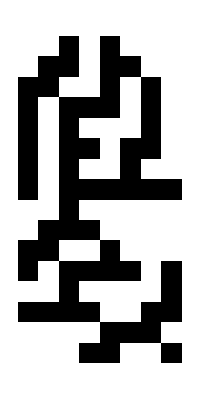

```mathematica
ArrayPlot[CellularAutomaton[30,data,15]]
```

If the rule is fixed, it still takes log_2(n) bits to convey the position of the read index. In this case 3 bits. This means that the data needs to be uniquely defined after 4 or less updates for any compression to occur.

```mathematica
2^8
```

256

```mathematica
2^5
```

32